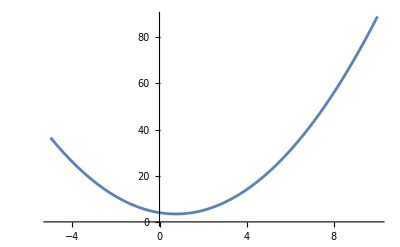

```mathematica
f[x_]:=4-1.5x+x^2;
range={-5,10,0.1};

Plot[f[x],{x, range[[1]], range[[2]]}]
```

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Join[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]

LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]

approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
errorFunc[xii_, w_]:=Quiet[With[{af=approxFunc[xii,w]},Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}]],General::munfl]
```

```mathematica
xiiRange=range;wRange=range; (*Tweak these for faster initial evaluation times *)

search[]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progress=PrintTemporary["0% Complete"];
numIterSearch=20;
Table[NotebookDelete[progress]; progress=PrintTemporary[ToString[Round[100*(iter-1)/numIterSearch]]<>"% Complete"]; search[], {iter,numIterSearch}]
```

{7.59314×10^11,14744.7,3443.97,2461.05,1734.03,1526.07,1458.88,1433.98,1423.72,1419.14,1416.99,1415.94,1415.43,1415.18,1415.05,1414.99,1414.95,1414.94,1414.93,1414.93}

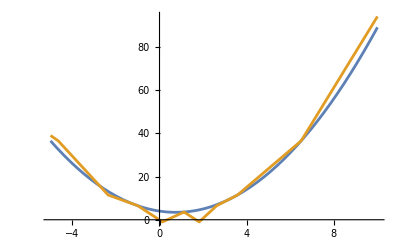

```mathematica
Plot[{f[x], (approxFunc@@minP)[(approxFunc@@minP)[x]]}, {x, range[[1]], range[[2]]}]
```

```mathematica
minP
```

{1.125,-0.999998}